```mathematica
Clear[AllData, ZoomedData,A,B]
```

```mathematica
AllData = Import["dataForWSMbandStructurem=4.dat"];
```

```mathematica
(** ZoomedData = Import["dataWSMZoomed+8and+6Irrationalm=4Parent32x32.dat"]; **)
```

```mathematica
(** B=Show[ListPlot[ZoomedData,PlotRange-> { All ,{-0.8,0.8}},PlotStyle->{PointSize[0.01],Black}],FrameTicks-> {{{π/2,""}},{-0.5,0.5},{},{}},BaseStyle-> 12,(** FrameLabel-> {"k_z","E"}, **)Frame-> True,RotateLabel-> False,FrameStyle->{{Thick, Black},{Thick, Black},{Thick, Black},{Thick, Black}},Axes->{True, False},
ImageSize-> 100] **)
```

```mathematica
Dimensions[AllData]
```

{102912,2}

```mathematica
FactorInteger[102912]
```

{{2,9},{3,1},{67,1}}

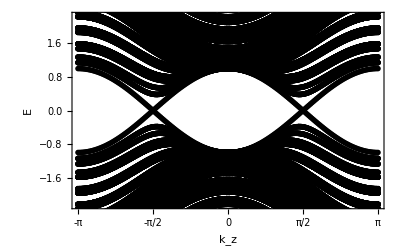

```mathematica
A=Show[ListPlot[AllData,PlotRange-> { {-π,π} ,{-2.25,2.25}},PlotStyle->{PointSize[0.01],Black}],
FrameLabel->{"k_z","E"},
FrameTicks-> {{-π,-π/2,0,π/2,π},Automatic,{},{}},BaseStyle-> 18,Frame-> True,RotateLabel-> False,FrameStyle->{{Thick, Black},{Thick, Black},{Thick, Black},{Thick, Black}},Axes->{True, False}
(**,
 Epilog-> Inset[B,{-0.2,-0.16}**)]
```